```mathematica
(*ref: Murphy, Fundamentals of light microscopy, p319*)
μm=10^-6;
nm=10^-9;
(*Diffraction limit. These eqs. are valid for NA > 0.7 *)
resXY[λ_,NA_]:=0.325 λ/(√2 NA^0.91)
resZ[λ_,RI_,NA_]:=0.532 λ/(√2)1/(RI-√(RI^2-NA^2))
```

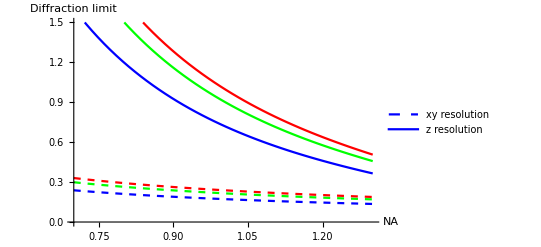

```mathematica
(*Resolution vs NA*)
RI=1.48;
Plot[Evaluate[Table[{resXY[λ nm,NA],resZ[λ nm,RI,NA]}/μm,{λ,{750, 940, 1040}}]],{NA,0.7,1.3},PlotRange->{0,1.5}, AxesLabel->{"NA","Diffraction limit"},PlotStyle->{{Dashed,Blue},Blue,{Dashed,Green},Green,{Dashed,Red},Red},PlotLegends->{"xy resolution","z resolution"}]
```

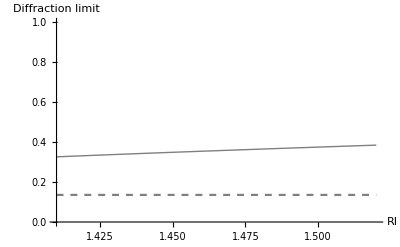

```mathematica
(*Resolution vs RI*)
NA=1.3;
λ=750 nm;
Plot[{resXY[λ,NA]/μm,resZ[λ,RI,NA]/μm},{RI,1.41,1.52},PlotRange->{0,1},PlotStyle->{{Dashed,Gray},{Thick,Gray}},AxesLabel->{"RI","Diffraction limit"}]
```